```mathematica
nthor[elist_,len_,x_]:=Block[{v=PadLeft[IntegerDigits[x,2],len]},Graph[Table[Piecewise[{{elist[[i]][[1]]->elist[[i]], □}, {□, □}}]
```

```mathematica
c5nthor[x_]:=Block[{v=PadLeft[IntegerDigits[x,2],10]},Graph[Flatten[Table[Piecewise[{{i->j, v[[1+i+(-3/2+j/2) j]]==0}, {j->i, True}}],{j,2,5},{i,1,j-1}],1]]]
```

```mathematica
Table[{n,Sum[1,{j,2,n},{i,1,j-1}]},{n,3,10}]
```

{{3,3},{4,6},{5,10},{6,15},{7,21},{8,28},{9,36},{10,45}}

```mathematica
InterpolatingPolynomial[%,n]
```

3+(3+1/2 (-4+n)) (-3+n)

```mathematica
cnnthor[n_,len_,x_]:=Block[{v=PadLeft[IntegerDigits[x,2],len]},Graph[Flatten[Table[Piecewise[{{i->j, v[[1+i+(-3/2+j/2) j]]==0}, {j->i, True}}],{j,2,n},{i,1,j-1}],1]]]
```

```mathematica
maxeig[g_]:=Max[Map[Abs,Eigenvalues[AdjacencyMatrix[g]]]]
```

```mathematica
maxeig2[g_]:=Max[Map[Re,Eigenvalues[AdjacencyMatrix[g]]]]
```

```mathematica
maxeig3[g_]:=Max[Map[Im,Eigenvalues[AdjacencyMatrix[g]]]]
```

```mathematica
numcy[g_]:=Length[FindCycle[g,∞,All]]
```

```mathematica
pr[g_]:={numcy[g],maxeig[g]}
```

```mathematica
pr2[g_]:={numcy[g],maxeig2[g]}
```

```mathematica
pr3[g_]:={numcy[g],maxeig3[g]}
```

```mathematica
pr[c5nthor[4]]
```

Max::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -Abs[Root[-1 - 2\ Slot[« 1 »] + Slot[« 1 »]^4 &, 3, 0]] + Abs[Root[-1 - 2\ #1 + #1^4 &, 4, 0]].

{3,Root[-1-2 #1+#1^4&,2]}

```mathematica
3+(3+1/2 (-4+5)) (-3+5)
```

10

```mathematica
prs[n_]:=Sort[DeleteDuplicates[Block[{len=3+(3+1/2 (-4+n)) (-3+n)},Table[pr[cnnthor[n,len,x]],{x,0,2^len-1}]]]]
```

```mathematica
Monitor[prs[5],x]
```

Max::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -Abs[Root[-1 - 2\ Slot[« 1 »] + Slot[« 1 »]^4 &, 3, 0]] + Abs[Root[-1 - 2\ #1 + #1^4 &, 4, 0]].

Max::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -Abs[Root[-1 - 3\ Slot[« 1 »] - 3\ Power[« 2 »] + Slot[« 1 »]^5 &, 2, 0]] + Abs[Root[-1 - 3\ #1 - 3\ Slot[« 1 »]^2 + #1^5 &, 3, 0]].

General::stop: Further output of Max :: meprec will be suppressed during this calculation.

{{0,0},{1,1},{3,Root[-1-2 #1+#1^4&,2]},{6,Root[-1-2 #1-3 #1^2+#1^5&,1]},{7,Root[-1-3 #1-3 #1^2+#1^5&,1]},{9,Root[-1-#1-#1^2+#1^3&,1]},{9,Root[-1-4 #1-4 #1^2+#1^5&,1]},{10,Root[-3-#1^2+#1^3&,1]},{12,2}}

```mathematica
Table[2^(10-5)*i,{i,0,32}]
```

{0,32,64,96,128,160,192,224,256,288,320,352,384,416,448,480,512,544,576,608,640,672,704,736,768,800,832,864,896,928,960,992,1024}

```mathematica
prs[n_,i_]:=Sort[DeleteDuplicates[Block[{len=3+(3+1/2 (-4+n)) (-3+n)},Table[pr[cnnthor[n,len,x]],{x,2^(len-5)*(i-1),2^(len-5)*i}]]]]
```

```mathematica
prs2[n_,i_]:=Sort[DeleteDuplicates[Block[{len=3+(3+1/2 (-4+n)) (-3+n)},Table[pr2[cnnthor[n,len,x]],{x,2^(len-5)*(i-1),2^(len-5)*i}]]]]
```

```mathematica
prs3[n_,i_]:=Sort[DeleteDuplicates[Block[{len=3+(3+1/2 (-4+n)) (-3+n)},Table[pr3[cnnthor[n,len,x]],{x,2^(len-5)*(i-1),2^(len-5)*i}]]]]
```

```mathematica
prs[5,1]
```

Max::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -Abs[Root[-1 - 2\ Slot[« 1 »] + Slot[« 1 »]^4 &, 3, 0]] + Abs[Root[-1 - 2\ #1 + #1^4 &, 4, 0]].

Max::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -Abs[Root[-1 - 3\ Slot[« 1 »] - 3\ Power[« 2 »] + Slot[« 1 »]^5 &, 2, 0]] + Abs[Root[-1 - 3\ #1 - 3\ Slot[« 1 »]^2 + #1^5 &, 3, 0]].

General::stop: Further output of Max :: meprec will be suppressed during this calculation.

{{0,0},{1,1},{3,Root[-1-2 #1+#1^4&,2]},{6,Root[-1-2 #1-3 #1^2+#1^5&,1]},{7,Root[-1-3 #1-3 #1^2+#1^5&,1]},{9,Root[-1-4 #1-4 #1^2+#1^5&,1]}}

```mathematica
pprs[n_]:=Table[ParallelSubmit[{i},prs[n,i]],{i,1,32}]
pprs2[n_]:=Table[ParallelSubmit[{i},prs2[n,i]],{i,1,32}]
pprs3[n_]:=Table[ParallelSubmit[{i},prs2[n,i]],{i,1,32}]
```

```mathematica
pprs[4]
r4=Sort[DeleteDuplicates[Flatten[WaitAll[%],1]]]
```

{prs[4,1]
,prs[4,2]
,prs[4,3]
,prs[4,4]
,prs[4,5]
,prs[4,6]
,prs[4,7]
,prs[4,8]
,prs[4,9]
,prs[4,10]
,prs[4,11]
,prs[4,12]
,prs[4,13]
,prs[4,14]
,prs[4,15]
,prs[4,16]
,prs[4,17]
,prs[4,18]
,prs[4,19]
,prs[4,20]
,prs[4,21]
,prs[4,22]
,prs[4,23]
,prs[4,24]
,prs[4,25]
,prs[4,26]
,prs[4,27]
,prs[4,28]
,prs[4,29]
,prs[4,30]
,prs[4,31]
,prs[4,32]
}

Max::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -Abs[Root[-1 - 2\ Slot[« 1 »] + Slot[« 1 »]^4 &, 3, 0]] + Abs[Root[-1 - 2\ #1 + #1^4 &, 4, 0]].

General::stop: Further output of Max :: meprec will be suppressed during this calculation.

{{0,0},{1,1},{3,Root[-1-2 #1+#1^4&,2]}}

```mathematica
pprs[5]
r5=Sort[DeleteDuplicates[Flatten[WaitAll[%],1]]]
```

{prs[5,1]
,prs[5,2]
,prs[5,3]
,prs[5,4]
,prs[5,5]
,prs[5,6]
,prs[5,7]
,prs[5,8]
,prs[5,9]
,prs[5,10]
,prs[5,11]
,prs[5,12]
,prs[5,13]
,prs[5,14]
,prs[5,15]
,prs[5,16]
,prs[5,17]
,prs[5,18]
,prs[5,19]
,prs[5,20]
,prs[5,21]
,prs[5,22]
,prs[5,23]
,prs[5,24]
,prs[5,25]
,prs[5,26]
,prs[5,27]
,prs[5,28]
,prs[5,29]
,prs[5,30]
,prs[5,31]
,prs[5,32]
}

Max::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -Abs[Root[-1 - 2\ Slot[« 1 »] + Slot[« 1 »]^4 &, 3, 0]] + Abs[Root[-1 - 2\ #1 + #1^4 &, 4, 0]].

Max::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -Abs[Root[-1 - 3\ Slot[« 1 »] - 3\ Power[« 2 »] + Slot[« 1 »]^5 &, 2, 0]] + Abs[Root[-1 - 3\ #1 - 3\ Slot[« 1 »]^2 + #1^5 &, 3, 0]].

General::stop: Further output of Max :: meprec will be suppressed during this calculation.

{{0,0},{1,1},{3,Root[-1-2 #1+#1^4&,2]},{6,Root[-1-2 #1-3 #1^2+#1^5&,1]},{7,Root[-1-3 #1-3 #1^2+#1^5&,1]},{9,Root[-1-#1-#1^2+#1^3&,1]},{9,Root[-1-4 #1-4 #1^2+#1^5&,1]},{10,Root[-3-#1^2+#1^3&,1]},{12,2}}

```mathematica
pprs[6]
r6=Sort[DeleteDuplicates[Flatten[WaitAll[%],1]]]
```

{prs[6,1]
,prs[6,2]
,prs[6,3]
,prs[6,4]
,prs[6,5]
,prs[6,6]
,prs[6,7]
,prs[6,8]
,prs[6,9]
,prs[6,10]
,prs[6,11]
,prs[6,12]
,prs[6,13]
,prs[6,14]
,prs[6,15]
,prs[6,16]
,prs[6,17]
,prs[6,18]
,prs[6,19]
,prs[6,20]
,prs[6,21]
,prs[6,22]
,prs[6,23]
,prs[6,24]
,prs[6,25]
,prs[6,26]
,prs[6,27]
,prs[6,28]
,prs[6,29]
,prs[6,30]
,prs[6,31]
,prs[6,32]
}

Max::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -Abs[Root[-1 - 2\ Slot[« 1 »] + Slot[« 1 »]^4 &, 3, 0]] + Abs[Root[-1 - 2\ #1 + #1^4 &, 4, 0]].

Max::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -Abs[Root[-1 - 3\ Slot[« 1 »] - 3\ Power[« 2 »] + Slot[« 1 »]^5 &, 2, 0]] + Abs[Root[-1 - 3\ #1 - 3\ Slot[« 1 »]^2 + #1^5 &, 3, 0]].

General::stop: Further output of Max :: meprec will be suppressed during this calculation.

{{0,0},{1,1},{2,1},{3,Root[-1-2 #1+#1^4&,2]},{6,Root[-1-2 #1-3 #1^2+#1^5&,1]},{7,Root[-1-3 #1-3 #1^2+#1^5&,1]},{9,Root[-1-#1-#1^2+#1^3&,1]},{9,Root[-1-4 #1-4 #1^2+#1^5&,1]},{10,Root[-3-#1^2+#1^3&,1]},{10,Root[-1-#1-#1^2+#1^3&,1]},{12,2},{12,Root[-1-3 #1-4 #1^2-4 #1^3+#1^6&,2]},{15,Root[-1-4 #1-6 #1^2-4 #1^3+#1^6&,2]},{16,Root[-1-4 #1-6 #1^2-5 #1^3+#1^6&,2]},{16,Root[-1-4 #1-5 #1^2-5 #1^3+#1^6&,2]},{20,Root[-1-5 #1-#1^3+#1^4&,2]},{20,Root[-2-4 #1-#1^3+#1^4&,2]},{20,Root[-1-4 #1-7 #1^2-6 #1^3+#1^6&,2]},{21,Root[-1-5 #1-9 #1^2-6 #1^3+#1^6&,2]},{21,Root[-2-6 #1-7 #1^2-6 #1^3+#1^6&,2]},{22,Root[-1-3 #1-#1^2-#1^3+#1^4&,2]},{22,Root[-2-6 #1-7 #1^2-6 #1^3+#1^6&,2]},{23,Root[-2-6 #1-7 #1^2-6 #1^3+#1^6&,2]},{26,Root[-2-7 #1-9 #1^2-7 #1^3+#1^6&,2]},{26,Root[-3-8 #1-7 #1^2-6 #1^3+#1^6&,2]},{27,Root[-2-7 #1-9 #1^2-7 #1^3+#1^6&,2]},{28,Root[-3-6 #1-#1^3+#1^4&,2]},{28,Root[-3-9 #1-8 #1^2-7 #1^3+#1^6&,2]},{31,1+√2},{32,Root[-2-8 #1-12 #1^2-8 #1^3+#1^6&,2]},{34,1+√2},{34,Root[-4-11 #1-10 #1^2-8 #1^3+#1^6&,2]}}

```mathematica
pprs2[6]
r62=Sort[DeleteDuplicates[Flatten[WaitAll[%],1]]]
```

{prs2[6,1]
,prs2[6,2]
,prs2[6,3]
,prs2[6,4]
,prs2[6,5]
,prs2[6,6]
,prs2[6,7]
,prs2[6,8]
,prs2[6,9]
,prs2[6,10]
,prs2[6,11]
,prs2[6,12]
,prs2[6,13]
,prs2[6,14]
,prs2[6,15]
,prs2[6,16]
,prs2[6,17]
,prs2[6,18]
,prs2[6,19]
,prs2[6,20]
,prs2[6,21]
,prs2[6,22]
,prs2[6,23]
,prs2[6,24]
,prs2[6,25]
,prs2[6,26]
,prs2[6,27]
,prs2[6,28]
,prs2[6,29]
,prs2[6,30]
,prs2[6,31]
,prs2[6,32]
}

Max::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -Re[Root[-1 - 4\ Slot[« 1 »] - 6\ Power[« 2 »] - 4\ Power[« 2 »] + Slot[« 1 »]^6 &, 3, 0]] + Re[Root[-1 - 4\ #1 - 6\ Slot[« 1 »]^2 - 4\ Slot[« 1 »]^3 + #1^6 &, 4, 0]].

Max::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -Re[Root[-1 - 4\ Slot[« 1 »] - 6\ Power[« 2 »] - 4\ Power[« 2 »] + Slot[« 1 »]^6 &, 5, 0]] + Re[Root[-1 - 4\ #1 - 6\ Slot[« 1 »]^2 - 4\ Slot[« 1 »]^3 + #1^6 &, 6, 0]].

Max::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -Re[Root[-1 - 3\ Slot[« 1 »] - 4\ Power[« 2 »] - 4\ Power[« 2 »] + Slot[« 1 »]^6 &, 3, 0]] + Re[Root[-1 - 3\ #1 - 4\ Slot[« 1 »]^2 - 4\ Slot[« 1 »]^3 + #1^6 &, 4, 0]].

General::stop: Further output of Max :: meprec will be suppressed during this calculation.

{{0,0},{1,1},{2,1},{3,Root[-1-2 #1+#1^4&,2]},{6,Root[-1-2 #1-3 #1^2+#1^5&,1]},{7,Root[-1-3 #1-3 #1^2+#1^5&,1]},{9,Root[-1-#1-#1^2+#1^3&,1]},{9,Root[-1-4 #1-4 #1^2+#1^5&,1]},{10,Root[-3-#1^2+#1^3&,1]},{10,Root[-1-#1-#1^2+#1^3&,1]},{12,2},{12,Root[-1-3 #1-4 #1^2-4 #1^3+#1^6&,2]},{15,Root[-1-4 #1-6 #1^2-4 #1^3+#1^6&,2]},{16,Root[-1-4 #1-6 #1^2-5 #1^3+#1^6&,2]},{16,Root[-1-4 #1-5 #1^2-5 #1^3+#1^6&,2]},{20,Root[-1-5 #1-#1^3+#1^4&,2]},{20,Root[-2-4 #1-#1^3+#1^4&,2]},{20,Root[-1-4 #1-7 #1^2-6 #1^3+#1^6&,2]},{21,Root[-1-5 #1-9 #1^2-6 #1^3+#1^6&,2]},{21,Root[-2-6 #1-7 #1^2-6 #1^3+#1^6&,2]},{22,Root[-1-3 #1-#1^2-#1^3+#1^4&,2]},{22,Root[-2-6 #1-7 #1^2-6 #1^3+#1^6&,2]},{23,Root[-2-6 #1-7 #1^2-6 #1^3+#1^6&,2]},{26,Root[-2-7 #1-9 #1^2-7 #1^3+#1^6&,2]},{26,Root[-3-8 #1-7 #1^2-6 #1^3+#1^6&,2]},{27,Root[-2-7 #1-9 #1^2-7 #1^3+#1^6&,2]},{28,Root[-3-6 #1-#1^3+#1^4&,2]},{28,Root[-3-9 #1-8 #1^2-7 #1^3+#1^6&,2]},{31,1+√2},{32,Root[-2-8 #1-12 #1^2-8 #1^3+#1^6&,2]},{34,1+√2},{34,Root[-4-11 #1-10 #1^2-8 #1^3+#1^6&,2]}}

```mathematica
pprs3[6]
r63=Sort[DeleteDuplicates[Flatten[WaitAll[%],1]]]
```

{prs2[6,1]
,prs2[6,2]
,prs2[6,3]
,prs2[6,4]
,prs2[6,5]
,prs2[6,6]
,prs2[6,7]
,prs2[6,8]
,prs2[6,9]
,prs2[6,10]
,prs2[6,11]
,prs2[6,12]
,prs2[6,13]
,prs2[6,14]
,prs2[6,15]
,prs2[6,16]
,prs2[6,17]
,prs2[6,18]
,prs2[6,19]
,prs2[6,20]
,prs2[6,21]
,prs2[6,22]
,prs2[6,23]
,prs2[6,24]
,prs2[6,25]
,prs2[6,26]
,prs2[6,27]
,prs2[6,28]
,prs2[6,29]
,prs2[6,30]
,prs2[6,31]
,prs2[6,32]
}

Max::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -Re[Root[-1 - 4\ Slot[« 1 »] - 6\ Power[« 2 »] - 4\ Power[« 2 »] + Slot[« 1 »]^6 &, 3, 0]] + Re[Root[-1 - 4\ #1 - 6\ Slot[« 1 »]^2 - 4\ Slot[« 1 »]^3 + #1^6 &, 4, 0]].

Max::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -Re[Root[-1 - 4\ Slot[« 1 »] - 6\ Power[« 2 »] - 4\ Power[« 2 »] + Slot[« 1 »]^6 &, 5, 0]] + Re[Root[-1 - 4\ #1 - 6\ Slot[« 1 »]^2 - 4\ Slot[« 1 »]^3 + #1^6 &, 6, 0]].

Max::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -Re[Root[-1 - 3\ Slot[« 1 »] - 4\ Power[« 2 »] - 4\ Power[« 2 »] + Slot[« 1 »]^6 &, 3, 0]] + Re[Root[-1 - 3\ #1 - 4\ Slot[« 1 »]^2 - 4\ Slot[« 1 »]^3 + #1^6 &, 4, 0]].

General::stop: Further output of Max :: meprec will be suppressed during this calculation.

{{0,0},{1,1},{2,1},{3,Root[-1-2 #1+#1^4&,2]},{6,Root[-1-2 #1-3 #1^2+#1^5&,1]},{7,Root[-1-3 #1-3 #1^2+#1^5&,1]},{9,Root[-1-#1-#1^2+#1^3&,1]},{9,Root[-1-4 #1-4 #1^2+#1^5&,1]},{10,Root[-3-#1^2+#1^3&,1]},{10,Root[-1-#1-#1^2+#1^3&,1]},{12,2},{12,Root[-1-3 #1-4 #1^2-4 #1^3+#1^6&,2]},{15,Root[-1-4 #1-6 #1^2-4 #1^3+#1^6&,2]},{16,Root[-1-4 #1-6 #1^2-5 #1^3+#1^6&,2]},{16,Root[-1-4 #1-5 #1^2-5 #1^3+#1^6&,2]},{20,Root[-1-5 #1-#1^3+#1^4&,2]},{20,Root[-2-4 #1-#1^3+#1^4&,2]},{20,Root[-1-4 #1-7 #1^2-6 #1^3+#1^6&,2]},{21,Root[-1-5 #1-9 #1^2-6 #1^3+#1^6&,2]},{21,Root[-2-6 #1-7 #1^2-6 #1^3+#1^6&,2]},{22,Root[-1-3 #1-#1^2-#1^3+#1^4&,2]},{22,Root[-2-6 #1-7 #1^2-6 #1^3+#1^6&,2]},{23,Root[-2-6 #1-7 #1^2-6 #1^3+#1^6&,2]},{26,Root[-2-7 #1-9 #1^2-7 #1^3+#1^6&,2]},{26,Root[-3-8 #1-7 #1^2-6 #1^3+#1^6&,2]},{27,Root[-2-7 #1-9 #1^2-7 #1^3+#1^6&,2]},{28,Root[-3-6 #1-#1^3+#1^4&,2]},{28,Root[-3-9 #1-8 #1^2-7 #1^3+#1^6&,2]},{31,1+√2},{32,Root[-2-8 #1-12 #1^2-8 #1^3+#1^6&,2]},{34,1+√2},{34,Root[-4-11 #1-10 #1^2-8 #1^3+#1^6&,2]}}

```mathematica
pprs[7]
r7=Sort[DeleteDuplicates[Flatten[WaitAll[%],1]]]
```

{prs[7,1]
,prs[7,2]
,prs[7,3]
,prs[7,4]
,prs[7,5]
,prs[7,6]
,prs[7,7]
,prs[7,8]
,prs[7,9]
,prs[7,10]
,prs[7,11]
,prs[7,12]
,prs[7,13]
,prs[7,14]
,prs[7,15]
,prs[7,16]
,prs[7,17]
,prs[7,18]
,prs[7,19]
,prs[7,20]
,prs[7,21]
,prs[7,22]
,prs[7,23]
,prs[7,24]
,prs[7,25]
,prs[7,26]
,prs[7,27]
,prs[7,28]
,prs[7,29]
,prs[7,30]
,prs[7,31]
,prs[7,32]
}

Max::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -Abs[Root[-1 - 2\ Slot[« 1 »] + Slot[« 1 »]^4 &, 3, 0]] + Abs[Root[-1 - 2\ #1 + #1^4 &, 4, 0]].

Max::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -Abs[Root[-1 - 3\ Slot[« 1 »] - 3\ Power[« 2 »] + Slot[« 1 »]^5 &, 2, 0]] + Abs[Root[-1 - 3\ #1 - 3\ Slot[« 1 »]^2 + #1^5 &, 3, 0]].

General::stop: Further output of Max :: meprec will be suppressed during this calculation.

$Aborted

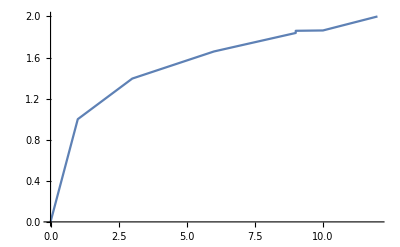

```mathematica
ListPlot[Sort[%],Joined->True]
```

```mathematica
Sort[DeleteDuplicates[Monitor[Table[pr[c5nthor[s]],{s,0,2^10-1}],s]]]
```

Max::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -Abs[Root[-1 - 2\ Slot[« 1 »] + Slot[« 1 »]^4 &, 3, 0]] + Abs[Root[-1 - 2\ #1 + #1^4 &, 4, 0]].

Max::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -Abs[Root[-1 - 3\ Slot[« 1 »] - 3\ Power[« 2 »] + Slot[« 1 »]^5 &, 2, 0]] + Abs[Root[-1 - 3\ #1 - 3\ Slot[« 1 »]^2 + #1^5 &, 3, 0]].

General::stop: Further output of Max :: meprec will be suppressed during this calculation.

{{0,0},{1,1},{3,Root[-1-2 #1+#1^4&,2]},{6,Root[-1-2 #1-3 #1^2+#1^5&,1]},{7,Root[-1-3 #1-3 #1^2+#1^5&,1]},{9,Root[-1-#1-#1^2+#1^3&,1]},{9,Root[-1-4 #1-4 #1^2+#1^5&,1]},{10,Root[-3-#1^2+#1^3&,1]},{12,2}}

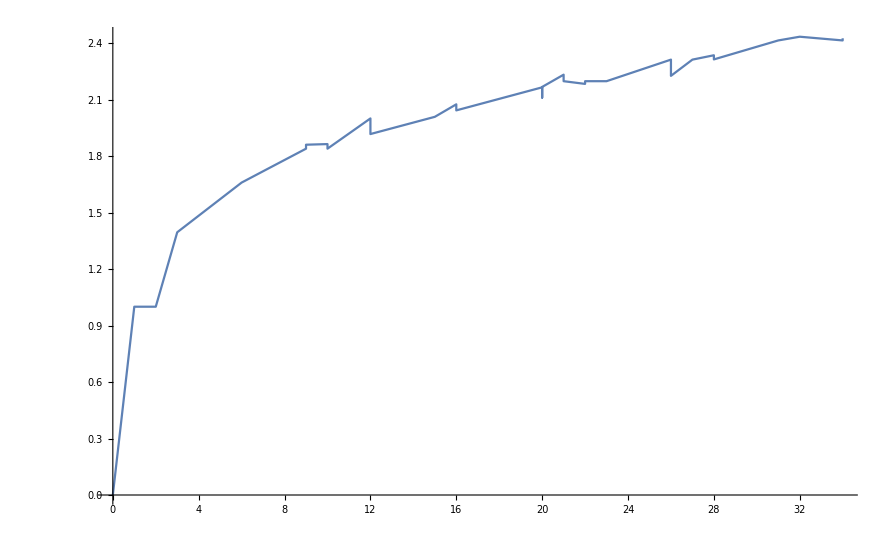

```mathematica
ListPlot[Sort[r6],Joined->True]
```

```mathematica
Map[N,r6]
```

{{0.,0.},{1.,1.},{2.,1.},{3.,1.39534},{6.,1.6593},{7.,1.71939},{9.,1.83929},{9.,1.8604},{10.,1.86371},{10.,1.83929},{12.,2.},{12.,1.91701},{15.,2.00849},{16.,2.07489},{16.,2.04272},{20.,2.16513},{20.,2.11063},{20.,2.16726},{21.,2.23236},{21.,2.19777},{22.,2.18338},{22.,2.19777},{23.,2.19777},{26.,2.3123},{26.,2.22606},{27.,2.3123},{28.,2.3355},{28.,2.31346},{31.,2.41421},{32.,2.43397},{34.,2.41421},{34.,2.42567}}

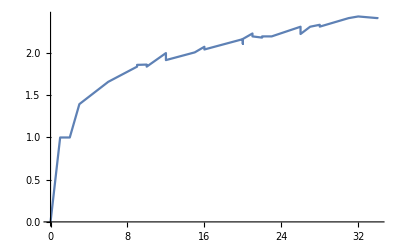

```mathematica
ListPlot[Sort[r62],Joined->True]
```

```mathematica
ListPlot[Sort[r63],Joined->True]
```

-Graphics-

```mathematica
Map[N,r62]
```

{{0.,0.},{1.,1.},{2.,1.},{3.,1.39534},{6.,1.6593},{7.,1.71939},{9.,1.83929},{9.,1.8604},{10.,1.86371},{10.,1.83929},{12.,2.},{12.,1.91701},{15.,2.00849},{16.,2.07489},{16.,2.04272},{20.,2.16513},{20.,2.11063},{20.,2.16726},{21.,2.23236},{21.,2.19777},{22.,2.18338},{22.,2.19777},{23.,2.19777},{26.,2.3123},{26.,2.22606},{27.,2.3123},{28.,2.3355},{28.,2.31346},{31.,2.41421},{32.,2.43397},{34.,2.41421},{34.,2.42567}}

```mathematica
Map[N,r63]
```

{{0.,0.},{1.,1.},{2.,1.},{3.,1.39534},{6.,1.6593},{7.,1.71939},{9.,1.83929},{9.,1.8604},{10.,1.86371},{10.,1.83929},{12.,2.},{12.,1.91701},{15.,2.00849},{16.,2.07489},{16.,2.04272},{20.,2.16513},{20.,2.11063},{20.,2.16726},{21.,2.23236},{21.,2.19777},{22.,2.18338},{22.,2.19777},{23.,2.19777},{26.,2.3123},{26.,2.22606},{27.,2.3123},{28.,2.3355},{28.,2.31346},{31.,2.41421},{32.,2.43397},{34.,2.41421},{34.,2.42567}}